```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Ed\GitHub\Wavelets

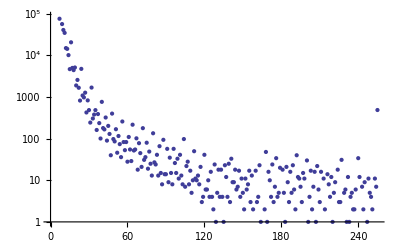

```mathematica
collageLengthData=Import["collage.data.length.freq"];
ListLogPlot[collageLengthData]
```

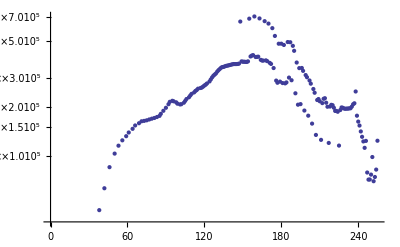

```mathematica
collageValueData=Import["collage.data.value.freq"];
ListLogPlot[collageValueData]
```

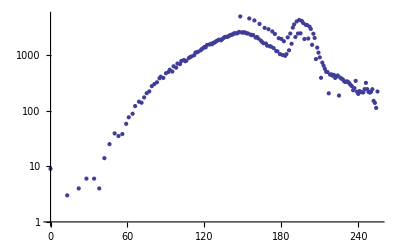

```mathematica
banffValueData=Import["banff.data.value.freq"];
ListLogPlot[banffValueData]
```

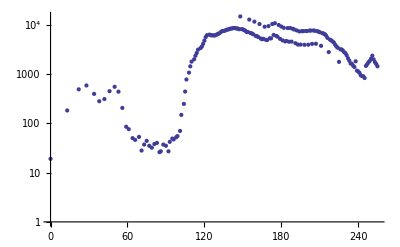

```mathematica
chicagoValueData=Import["chicago.data.value.freq"];
ListLogPlot[chicagoValueData]
```

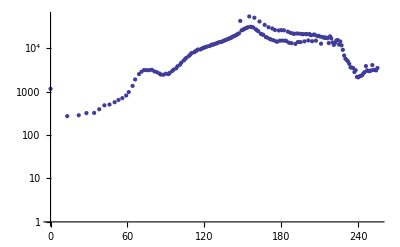

```mathematica
haleakalaValueData=Import["haleakala.data.value.freq"];
ListLogPlot[haleakalaValueData]
```

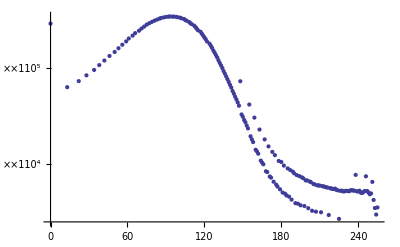

```mathematica
hubbleValueData=Import["hubble.data.value.freq"];
ListLogPlot[hubbleValueData]
```

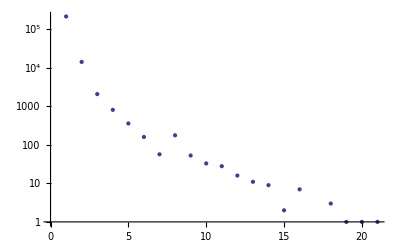

```mathematica
banffLengthData=Import["banff.data.length.freq"];
ListLogPlot[banffLengthData]
```

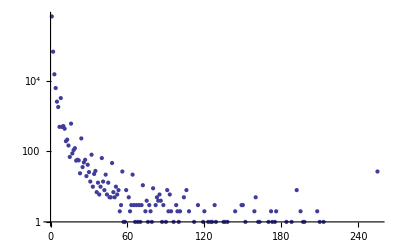

```mathematica
chicagoLengthData=Import["chicago.data.length.freq"];
ListLogPlot[chicagoLengthData]
```

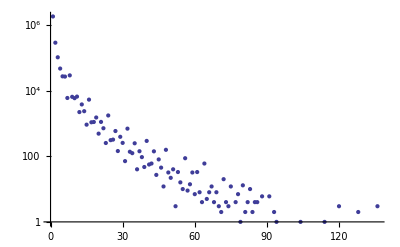

```mathematica
haleakalaLengthData=Import["haleakala.data.length.freq"];
ListLogPlot[haleakalaLengthData]
```

```mathematica
lenna1=Import["lenna_values.csv"];
lenna2=Import["lenna_values2.csv"];
lenna1=Transpose[lenna1][[1]];
lenna2=Transpose[lenna2][[1]];
```

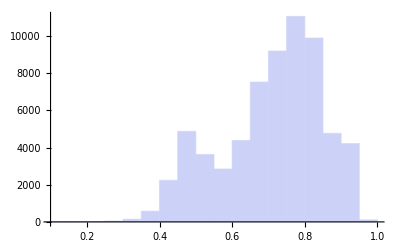

```mathematica
Histogram[lenna1,25]
```

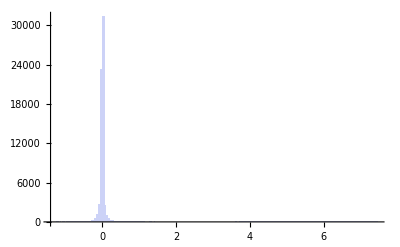

```mathematica
Histogram[lenna2]
```

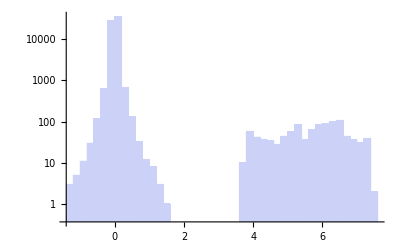

```mathematica
Histogram[lenna2,50,ScalingFunctions->"Log"]
```

```mathematica
quad= Transpose[Import["quad.csv"]][[1]];
```

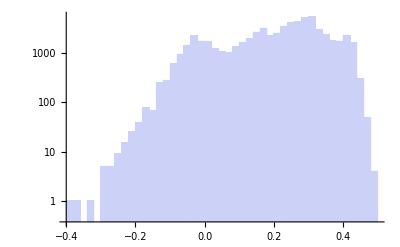

```mathematica
Histogram[quad,50, ScalingFunctions->"Log"]
```

```mathematica
quad=Transpose[Import["quad.csv"]][[1]];
quad0=Transpose[Import["quad0.csv"]][[1]];
quad10=Transpose[Import["quad10.csv"]][[1]];
quad11=Transpose[Import["quad11.csv"]][[1]];
quad01=Transpose[Import["quad01.csv"]][[1]];
quad20=Transpose[Import["quad20.csv"]][[1]];
quad22=Transpose[Import["quad22.csv"]][[1]];
quad02=Transpose[Import["quad02.csv"]][[1]];
quad30=Transpose[Import["quad30.csv"]][[1]];
quad33=Transpose[Import["quad33.csv"]][[1]];
quad03=Transpose[Import["quad03.csv"]][[1]];
```

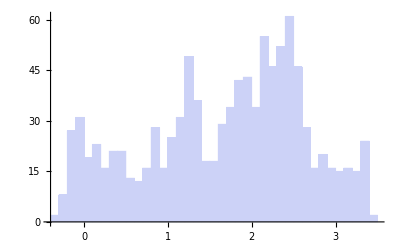

```mathematica
Histogram[quad0, 50]
```

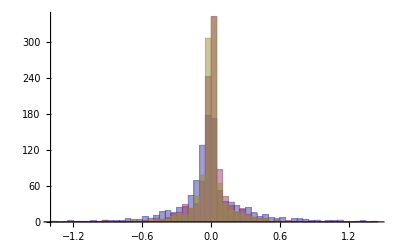

```mathematica
Histogram[{quad10, quad01, quad11}, 50]
```

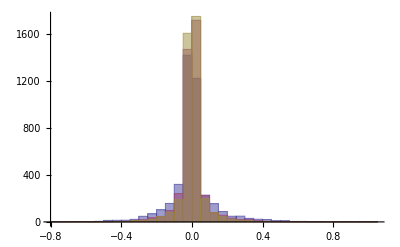

```mathematica
Histogram[{quad20, quad02, quad22}, 50]
```

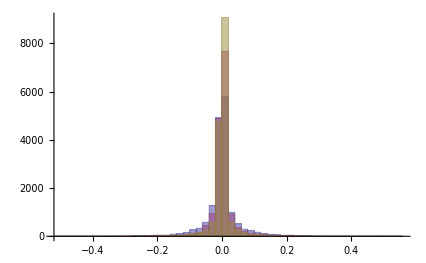

```mathematica
Histogram[{quad30, quad03, quad33}, 50]
```

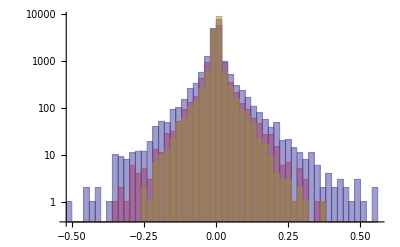

```mathematica
Histogram[{quad30, quad03, quad33}, 50, ScalingFunctions->"Log"]
```

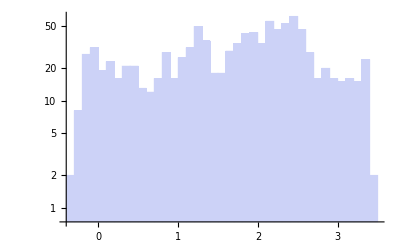

```mathematica
Histogram[quad0,50, ScalingFunctions->"Log"]
```

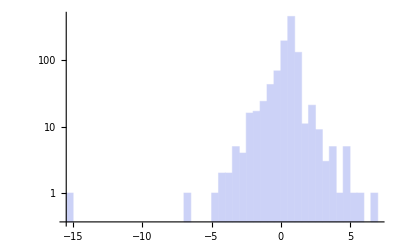

```mathematica
Histogram[Function[{x}, Sign[x]Log[Abs[x]]] /@ quad0,50, ScalingFunctions->"Log"]
```

```mathematica
Function[{x}, If[x==0,0,Sign[x]Log[Abs[x]]] ]/@ {-3,-2,-1,-.5,0,.5,1,2,3}
```

{-Log[3],-Log[2],0,0.693147,0,-0.693147,0,Log[2],Log[3]}

```mathematica
{Mean[#],StandardDeviation[#]} &/@ {quad,(#-1.672)(.1/.955645)& /@ quad0, quad01, quad10,quad11,quad20,quad02,quad22,quad30,quad03,quad33}//MatrixForm
```

(0.0258558 | 0.24971
6.47475×10^-6 | 0.1
0.00420496 | 0.160105
-0.00761049 | 0.303032
-0.000624232 | 0.140412
-0.00236912 | 0.125433
0.00121783 | 0.0779191
-0.000701783 | 0.0627707
-0.000884412 | 0.0566903
0.000345148 | 0.0363259
0.00017377 | 0.028118)

```mathematica
Length[quad]
```

65536

Average